# Log analysis 20231001 - 20231007

## Title: CiNiiのログから見るユーザーアクセスグラフの計量分析

### 情報知識学会抄録

```mathematica
submittext=
"NIIではCiNii（およびその他関連サービス）のログを分析するための専用環境「統合ログ基盤」を整備してきた。本発表では当該基盤の整備について、および当該基盤の機能を使ったログ分析結果の一部を紹介する。整備については構成したシステムの概要・性能の紹介を行う。ログ分析については当該基盤の特徴的な機能である、ユーザーストーリーを意識したユーザーアクションを「ボキャブラリ」として各アクセスURL（ログ）に付与する機能、リファラーとアクセスの連鎖をつなげた「リファラーグラフ」を生成する機能、を利用した分析を中心に報告する。本研究におけるリファラーグラフは個々の（推定）ユーザーの行動を端的に捉えるものとして利用できるものである。"
```

NIIではCiNii（およびその他関連サービス）のログを分析するための専用環境「統合ログ基盤」を整備してきた。本発表では当該基盤の整備について、および当該基盤の機能を使ったログ分析結果の一部を紹介する。整備については構成したシステムの概要・性能の紹介を行う。ログ分析については当該基盤の特徴的な機能である、ユーザーストーリーを意識したユーザーアクションを「ボキャブラリ」として各アクセスURL（ログ）に付与する機能、リファラーとアクセスの連鎖をつなげた「リファラーグラフ」を生成する機能、を利用した分析を中心に報告する。本研究におけるリファラーグラフは個々の（推定）ユーザーの行動を端的に捉えるものとして利用できるものである。

```mathematica
StringLength[submittext]
```

313

## 対象期間：20231001 - 20231007

単日で行った分析結果のsaveを読み込み、1 W分の分析を行う。

## コンセプト

アクセスログから分離したユーザーごとのアクセスグラフを一種のプロダクトとみなし、計量書誌学の観点から分析を行う。

用語：
アクセス：ログのアクセスURL
（アクセス）連鎖：リファラー -> アクセスURLとなる”エッジ”およびエッジが連なった”経路”または”グラフ” => グラフの場合はReferrer Graph[1] というらしい。
ユーザーアクセスグラフ：単一ユーザー（推定）によるアクセスのグラフ
ボキャブラリ：アクセスの性質・アクションを端的に表す単語

分析項目の候補：

ユーザーアクセスグラフの規模クラス内のメンバの分布（Zipを仮定）、1日/1週間/3ヶ月

クラスのメンバ数の分布が対象になるのでクラスを作る。（例：被引用が1件のクラス）

vertex数クラス

edge数クラス

リファラーと離脱次のURLのボキャブラリのペア

離脱時のURL（voc）/初回アクセスのドメイン

ボキャブラリ“detail”が付与される、タイムライン内のノードの位置

ボキャブラリ”detail”が付与されるノードの割合（高いほど効率的と仮定）

どのくらいのユーザーが”detail”まで確認しているか？

NIIサービス連携がどのくらいあるか？

滞留時間は精度がよくないので発表としては使わない？

ユーザーアクセスグラフの類型

プロパティ：voc出現（重み付き/重みなし）

プロパティ：vocによるアクセスグラフ（重み付き/重みなし）のスペクトル

非対称行列（隣接行列そのまま）のスペクトル

キルヒホフ行列のスペクトル（undirectedの場合重みなしとなる）

N次の連鎖

アクセスグラフの類型ごとのメンバー数がZip型分布に従うか？

アクセスグラフの類型をクラスタリングし類型間の関係を確認する

クラスタリング法は？使用する類型のプロパティは？

分析を組み合わせ、各々の類型がどのような行動パターンか説明可能か？

参照：

1. B. de la Ossa, A. Pont, J. Sahuquillo, J. A. Gil ; “Referrer graph: a low-cost web prediction algorithm” ; Proceedings of the 2010 ACM Symposium on Applied ComputingMarch 2010Pages 831–838 ; https://doi.org/10.1145/1774088.1774260

```mathematica
Grid[Import["/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/analysis_items.xlsx"][[1]],ItemSize->Full,Frame->All]
```

CiNiiのログから見るユーザーアクセスグラフの計量分析 |  |  |  |  |  |  |  |  |  |  |  |  | 
分析項目の整理 |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 分析項目→ | ユーザーアクセスグラフの構成 | グラフの規模 | voc[detail]のグラフ内の位置 | リファラーと離脱時のアクセスURL(voc) | グラフのN次の連鎖パス | グラフに出現するvocのリスト | vocグラフスペクトル | 滞在/滞留時間 | 連携アクセス |  | [今後]キーワード分析 | [間に合うか？]グラフ使わないクロス集計
 | 目的→ | 分析の基本となるグラフを構成する | グラフの規模の分布を確認する | ・ユーザーがdetailページに辿り着いているか | ・各グラフにおける典型的な行動を捉える | ・各グラフにおける典型的な行動を捉える
・パスの規模の分布を確認する | ・グラフを類型化する
・グラフ類型のクラスタリング
・グラフ類型の規模の分布を確認する | ・グラフを類型化する
・グラフ類型のクラスタリング
・グラフ類型の規模の分布を確認する |  | ・ciと他基盤の連携グラフがどの程度あるか |  |  | 
 | コメント→ |  |  |  |  |  | 0/1出現を利用してクラスを決定
クラスを対象としてクラスタリング | グラフの固有値列を用いてクラスを決定
クラスを対象としてクラスタリング |  |  |  |  | ・リファラーと...
・組織と...
 | グラフタイプ↓/グラフから何を確認すれば良いか→ |  |  |  |  |  |  |  |  |  |  |  | 
 | Basic-graph
リファラー -> アクセスURLの連鎖による有向グラフ | グラフを構成 | - | - | - | - | - | - |  | - |  |  | 
 | voc-label-graph
上記のグラフのvertexにvocを付与したもの | Basic-graphからvoc-label-graphを構成 | ・Vertex
・Edge | ・グラフ内のvertexを最終アクセス時刻順に並べてdetailがどの位置にあるか | ・グラフ内の最初のリファラー
・グラフ内で最後にアクセスしたURL | ・最大連鎖長をグラフごとに取る
・1次（Vertex）
・2次（Edge）
・3次
・何次まで？ | ・重みつきvocリスト
・重みなしvocリスト | - | ・滞留時間：グラフ内vertexのアクセス時刻のMaxとMinの差
・滞在時間：グラフ内vertexをアクセス時刻順に並べ時間間隔を算出したもの | ・条件付きエッジ（リファラーもしくはリクエストURLのvocがci以外を含む、かつciを含む） |  |  | 
 | voc-graph
上記のグラフのvertexをすべてvocに振り直してシュリンクさせたもの | Basic-graphからvoc-graphを構成 | - |  | - | - | - | ・キルヒホフグラフの固有値列 |  | - |  |  | 
 | Saveの対象
(N)

保存先ファイル | ・voc-label-graph
・voc-graph（3種）
(N=グラフ数)

保存先はそれぞれ分ける | ・VertexList
・EdgeList
・Vertex数
・Edge数
(N=グラフ数)

一つのファイル | ・vocが"detail"であるposition <= VertexListとして保存
(N=グラフ数)

左と同じファイル | ・各グラフの最初のリファラーと最後のアクセスURLのペア <= VertexListとして保存
・上記に対するvoc <= VertexListとして保存
(N=グラフ数)

左と同じファイル | ・[保留]voc-label-graphのlongest-path
(N=グラフ数)

保存しない | ・重みつきvoc出現リスト(要素数固定ベクトル)
・重みなしvoc出現リスト(要素数固定ベクトル)
(N=グラフ数)

一つのファイル | ・キルヒホフ行列
・キルヒホフ行列の固有値列
(N=グラフ数)

一つのファイル | ・グラフ滞留時間(一つの値)：グラフ内vertexのアクセス時刻のMaxとMinの差
・ページ滞在時間(リスト)：グラフ内vertexをアクセス時刻順に並べ時間間隔を算出したもの

一つのファイル |  |  |  |

## Target ID

```mathematica
tIDs=Table[n,{n,7}]
```

{1,2,3,4,5,6,7}

## Settings

```mathematica
basedir="/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/

```mathematica
datadir=basedir<>"D=*/T=4/_story/"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=*/T=4/_story/

```mathematica
fileDirs=FileNames[datadir]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231008/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231009/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231010/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231011/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231012/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231013/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231014/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231015/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231016/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231017/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231018/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231019/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231020/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231021/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231022/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231023/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231024/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231025/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231026/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231027/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231028/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231029/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231030/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231031/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231101/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231102/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231103/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231104/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231105/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231106/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231107/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231108/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231109/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231110/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231111/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231112/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231113/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231114/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231115/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231116/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231117/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231118/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231119/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231120/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231121/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231122/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231123/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231124/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231125/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231126/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231127/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231128/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231129/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231130/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231201/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231202/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231203/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231204/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231205/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231206/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231207/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231208/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231209/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231210/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231211/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231212/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231213/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231214/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231215/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231216/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231217/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231218/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231219/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231220/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231221/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231222/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231223/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231224/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231225/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231226/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231227/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231228/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231229/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231230/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231231/T=4/_story}

```mathematica
fileDates=Map[StringSplit[#,{"/","="}][[10]]&,fileDirs]
```

{20231001,20231002,20231003,20231004,20231005,20231006,20231007,20231008,20231009,20231010,20231011,20231012,20231013,20231014,20231015,20231016,20231017,20231018,20231019,20231020,20231021,20231022,20231023,20231024,20231025,20231026,20231027,20231028,20231029,20231030,20231031,20231101,20231102,20231103,20231104,20231105,20231106,20231107,20231108,20231109,20231110,20231111,20231112,20231113,20231114,20231115,20231116,20231117,20231118,20231119,20231120,20231121,20231122,20231123,20231124,20231125,20231126,20231127,20231128,20231129,20231130,20231201,20231202,20231203,20231204,20231205,20231206,20231207,20231208,20231209,20231210,20231211,20231212,20231213,20231214,20231215,20231216,20231217,20231218,20231219,20231220,20231221,20231222,20231223,20231224,20231225,20231226,20231227,20231228,20231229,20231230,20231231}

```mathematica
vocdir="/Volumes/home/NII/togo-log/rcoslogs/voc/"
```

/Volumes/home/NII/togo-log/rcoslogs/voc/

## Edge & Vertex from voc-label graph

### エッジ+ノードカウントデータ

```mathematica
EVSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_EVcount.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_EVcount.save}

```mathematica
start=Now
Map[Get,EVSaveFile];
end=Now
end-start
```

Mon 4 Mar 2024 17:22:22GMT+9

Part::partw: Part 3 of {porntrex.com} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Mon 4 Mar 2024 17:24:38GMT+9

2.25943 min

### edge count

```mathematica
(storyEdgeSelW[4,"voc-edgecount"]["20231001-07"]=Apply[Join,Map[storyEdgeSel[4,"voc-edgecount"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{1143117}

エッジ数そのもののZipf分布(N(r)=C r^-a)を「一応」確認する：
aは1~3程度が通常、aが小さいほど均等。aはここから乖離しても構わない。

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffitW[4,"graph_edge"]["20231001-07"]=FindFit[Sort[storyEdgeSelW[4,"voc-edgecount"]["20231001-07"],#1>#2&],zipf[r],{c,a},r]
```

{c→11071.5,a→0.583885}

エッジ数クラスのメンバ数のZipf分布(N(r)=C r^-a)を確認する：
aは1~3程度が通常、aが小さいほど均等。

```mathematica
(tallysortW[4,"voc-edgecount-prod"]["20231001-07"]=Sort[Tally[storyEdgeSelW[4,"voc-edgecount"]["20231001-07"]],#1[[2]]>#2[[2]]&])//Dimensions
```

{704,2}

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffitW[4,"edge"]["20231001-07"]=FindFit[Map[#[[2]]&,tallysortW[4,"voc-edgecount-prod"]["20231001-07"]],zipf[r],{c,a},r]
```

{c→808478.,a→2.9119}

### vertex count

```mathematica
storyNodeSel[4,"voc-nodecount"][fileDates[[2]]]//Length
```

183802

```mathematica
(storyNodeSelW[4,"voc-nodecount"]["20231001-07"]=Apply[Join,Map[storyNodeSel[4,"voc-nodecount"][fileDates[[#]]]&,tIDs]])//Length
```

1143117

ノード数クラスのメンバ数のZipf分布(N(r)=C r^-a)を確認する：
aは1~3程度が通常、aが小さいほど均等。

```mathematica
(tallysortW[4,"voc-nodecount-prod"]["20231001-07"]=Sort[Tally[storyNodeSelW[4,"voc-nodecount"]["20231001-07"]],#1[[2]]>#2[[2]]&])//Dimensions
```

{463,2}

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffitW[4,"node"]["20231001-07"]=FindFit[Map[#[[2]]&,tallysortW[4,"voc-nodecount-prod"]["20231001-07"]],zipf[r],{c,a},r]
```

{c→851283.,a→2.91675}

### time-sorted vertex(mintime)

vocリスト中のdetailの位置

```mathematica
(vocDetailPosW[4]["20231001-07"]=Apply[Join,Map[vocDetailPos[4][fileDates[[#]]]&,tIDs]])//Length
```

1143117

およそ1割がdetailに到達しておらず、

```mathematica
(vocNoDetailPosW[4]["20231001-07"]=Sort[Cases[vocDetailPosW[4]["20231001-07"],x_/;x[[2]]=={}],#1[[1]]>#2[[1]]&])//Length
```

106525

さらにそのおよそ1割が多量アクセスを行っている。

```mathematica
Cases[vocNoDetailPosW[4]["20231001-07"],x_/;x[[1]]>=10]//Length
```

6613

### first-in last-out

グラフの最初のリファラー(ドメイン)と離脱次のvocのペア

```mathematica
storyNodePSel[4,"firstANDlast","voc","dropAccT","domain"][fileDates[[2]]]//Length
```

183802

```mathematica
(storyNodePSelW[4,"firstANDlast","voc","dropAccT","domain"]["20231001-07"]=Apply[Join,Map[storyNodePSel[4,"firstANDlast","voc","dropAccT","domain"][fileDates[[#]]]&,tIDs]])//Length
```

1143117

In - Out集計

```mathematica
(storyNodeInOutClassW[4]["20231001-07"]=Sort[Tally[storyNodePSelW[4,"firstANDlast","voc","dropAccT","domain"]["20231001-07"]],#1[[2]]>#2[[2]]&])//Dimensions
```

{6950,2}

```mathematica
storyNodeInOutClassW[4]["20231001-07"][[1;;40]]
```

{{{ci.nii.ac.jp,voc[ci:*,confirm,detail]},331229},{{www.google.com,voc[ci:*,confirm,detail]},193260},{{www.google.co.jp,voc[ci:*,confirm,detail]},91211},{{search.yahoo.co.jp,voc[ci:*,confirm,detail]},73609},{{scholar.google.com,voc[ci:*,confirm,detail]},65901},{{www.bing.com,voc[ci:*,confirm,detail]},41194},{{scholar.google.co.jp,voc[ci:*,confirm,detail]},29104},{{voc[ci:*,view,top],voc[ci:*,explore,all]},26735},{{voc[ci:*,explore,all],voc[ci:*,explore,all]},24533},{{www.google.com,voc[ci:*,explore,all]},17323},{{voc[ci:*,explore,all],voc[ci:*,confirm,detail]},17028},{{voc[ci:*,confirm,detail],voc[ci:*,confirm,detail]},14674},{{voc[ci:*,view,top],voc[ci:*,confirm,detail]},13130},{{search.jamas.or.jp,voc[ci:*,confirm,detail]},9814},{{voc[ci:*,search,articles],voc[ci:*,search,articles]},9770},{{www.google.com,voc[ci:*,view,top]},9536},{{www.bing.com,voc[ci:*,explore,all]},7059},{{www.google.co.jp,voc[ci:*,explore,all]},6639},{{kaken.nii.ac.jp,voc[ci:*,confirm,detail]},5934},{{ci.nii.ac.jp,voc[ci:*,view,top]},5879},{{voc[ci:*,confirm,detail],voc[ci:*,explore,all]},5837},{{voc[ci:*,search,articles],voc[ci:*,confirm,detail]},5680},{{voc[ci:*,view,top],voc[ci:*,search,articles]},5174},{{iss.ndl.go.jp,voc[ci:*,view,top]},4964},{{ci.nii.ac.jp,voc[ci:*,search,articles]},4841},{{www.google.co.jp,voc[ci:*,view,top]},4495},{{scholar.google.jp,voc[ci:*,confirm,detail]},4406},{{www.google.com,voc[ci:*,search,articles]},3858},{{search.yahoo.co.jp,voc[ci:*,explore,all]},3522},{{nrid.nii.ac.jp,voc[ci:*,confirm,detail]},3211},{{scholar.google.es,voc[ci:*,confirm,detail]},2975},{{t.co,voc[ci:*,confirm,detail]},2916},{{voc[ci:*,explore,all],voc[ci:*,search,articles]},2789},{{www.bing.com,voc[ci:*,search,articles]},2416},{{www.wikidata.org,voc[ci:*,confirm,detail]},2400},{{scholar.google.de,voc[ci:*,confirm,detail]},2042},{{search.yahoo.co.jp,voc[ci:*,view,top]},1835},{{voc[ci:*,request,api],voc[ci:*,search,articles]},1659},{{www.bing.com,voc[ci:*,view,top]},1601},{{www.google.co.jp,voc[ci:*,search,articles]},1564}}

### vocベクトルデータ

```mathematica
vocVecSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_vocVec.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_vocVec.save}

```mathematica
Get[vocVecSaveFile[[2]]];
```

```mathematica
start=Now
Map[Get,vocVecSaveFile];
end=Now
end-start
```

Mon 4 Mar 2024 17:32:17GMT+9

Mon 4 Mar 2024 17:35:38GMT+9

3.34128 min

### voc vector

```mathematica
storyVocAVecSel[4,"voc-only"][fileDates[[2]]]//Length
```

183802

重みなし(0/1)voc出現リスト

```mathematica
(storyVocAVecSelW[4,"voc-only"]["20231001-07"]=Apply[Join,Map[storyVocAVecSel[4,"voc-only"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{1143117,59}

### voc vectorクラスタリング

Tallyでクラスを作る

```mathematica
(storyVocAVecSelClassW[4,"voc-only"]["20231001-07"]=Sort[Tally[storyVocAVecSelW[4,"voc-only"]["20231001-07"]],#1[[2]]>=#2[[2]]&])//Dimensions
```

{498,2}

```mathematica
(storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-07"]=storyVocAVecSelClassW[4,"voc-only"]["20231001-07"][[1;;50]])//Dimensions
```

{50,2}

クラスのメンバー数の確認

```mathematica
Total[Map[#[[2]]&,storyVocAVecSelClassW[4,"voc-only"]["20231001-07"]]]
```

1143117

```mathematica
Total[Map[#[[2]]&,storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-07"]]]
```

1135239

```mathematica
1135239/1143117//N
```

0.993108

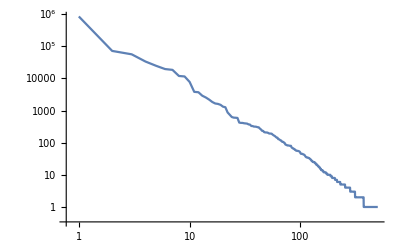

```mathematica
ListLogLogPlot[Map[#[[2]]&,storyVocAVecSelClassW[4,"voc-only"]["20231001-07"]],Joined->True]
```

クラスタリング前の分布の確認

すべてのクラス

```mathematica
(storyVocAVecSelClassPCAW[4,"voc-only"]["20231001-07"]=PrincipalComponents[N[Map[#[[1]]&,storyVocAVecSelClassW[4,"voc-only"]["20231001-07"]]]])//Dimensions
```

{498,59}

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocAVecSelClassPCAW[4,"voc-only"]["20231001-07"]]]
```

-Graphics3D-

メンバーの多いクラス上位50

```mathematica
(storyVocAVecSelClassPCAW[4,"voc-only","top50"]["20231001-07"]=PrincipalComponents[N[Map[#[[1]]&,storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-07"]]]])//Dimensions
```

{50,59}

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocAVecSelClassPCAW[4,"voc-only","top50"]["20231001-07"]]]
```

-Graphics3D-

上位50クラスを階層クラスタリング

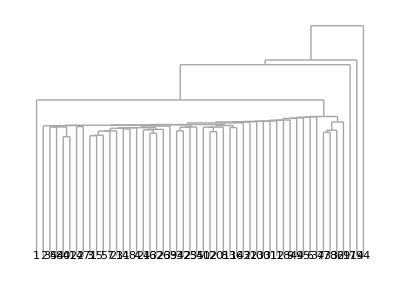

```mathematica
Dendrogram[storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-07"]->Table[n,{n,50}]]
```

### 滞在・滞留時間データ

```mathematica
accTimeSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_accTime.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_accTime.save}

```mathematica
start=Now
Map[Get,accTimeSaveFile];
end=Now
end-start
```

Mon 4 Mar 2024 17:49:27GMT+9

Mon 4 Mar 2024 17:49:53GMT+9

26.2954 s

```mathematica
(edgeAccTimeListW[4]["20231001-07"]=Apply[Join,Map[edgeAccTimeList[4,"stay"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{1143117}

## KirchhoffMatrix from voc graph

### キルヒホフ行列データ

```mathematica
KMSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_KM.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_KM.save}

```mathematica
start=Now
Map[Get,KMSaveFile];
end=Now
end-start
```

Mon 4 Mar 2024 17:50:45GMT+9

Mon 4 Mar 2024 18:00:38GMT+9

9.8731 min

### 固有値によるクラスタリング

キルヒホフ行列の固有値列

```mathematica
(storyVocGraphEva59W[4]["20231001-07"]=Apply[Join,Map[storyVocGraphEva59[4][fileDates[[#]]]&,tIDs]])//Dimensions
```

{1143117,59}

Tallyでクラスをつくる

```mathematica
(storyVocGraphEva59CLassW[4]["20231001-07"]=Sort[Tally[storyVocGraphEva59W[4]["20231001-07"]],#1[[2]]>#2[[2]]&])//Dimensions
```

{6510,2}

```mathematica
(storyVocGraphEva59CLassW[4]["20231001-07","top50"]=storyVocGraphEva59CLassW[4]["20231001-07"][[1;;50]])//Dimensions
```

{50,2}

クラスのメンバー数確認

```mathematica
Map[#[[2]]&,storyVocGraphEva59CLassW[4]["20231001-07"]]//Total
```

1143117

```mathematica
Map[#[[2]]&,storyVocGraphEva59CLassW[4]["20231001-07","top50"]]//Total
```

1124565

```mathematica
1124565/1143117//N
```

0.983771

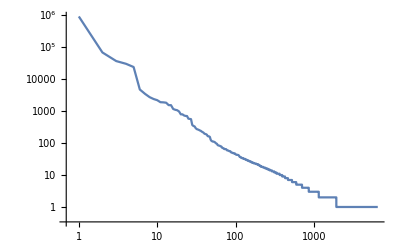

```mathematica
ListLogLogPlot[Map[#[[2]]&,storyVocGraphEva59CLassW[4]["20231001-07"]],Joined->True]
```

クラスタリング前の分布の確認

クラスの固有値列のPCA

```mathematica
Eva59ClassNum=(storyVocGraphEva59CLassPCAW[4]["20231001-07"]=PrincipalComponents[Map[#[[1]]&,storyVocGraphEva59CLassW[4]["20231001-07"]]])//Length
```

6510

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocGraphEva59CLassPCAW[4]["20231001-07"]]]
```

-Graphics3D-

上位50クラスをクラスタリング

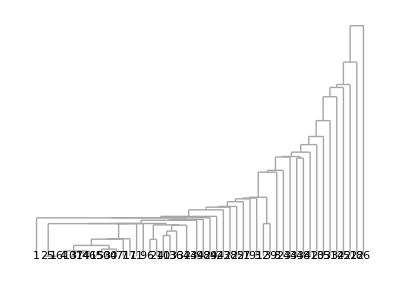

```mathematica
Dg=Dendrogram[   N[Map[#[[1]]&,storyVocGraphEva59CLassW[4]["20231001-07","top50"]]]   ->Table[n,{n,50}]   ]
```

## 属性のまとめ